```mathematica
(** Various helper functions for standard parts of the paper / reachable set results **)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
cmat[ab_, tau_, tf_] := MatrixExp[-(tau - tf) ab // Transpose][[4;;6, 1;;3]];
xrf[tf_, delta_, h_, deltaT_, A_, n_, Rr_, emax_] := NIntegrate[  emax (cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta / (deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt)[[1]]  ,{tau, 0, tf}];
x3fanalytical[tf_, h_, n_]:= h(2Floor[n tf / Pi]+1+ Mod[Floor[n tf / Pi], 2] Cos[n tf] - (Mod[Floor[n tf / Pi], 2] - 1)(- Cos[n tf]));
```

```mathematica
(** Computes the thrust-limited reachable set for a given final time **)
thrustreachable[xrf_,tf_, na_, emax_] := Module[{points, tfs, hs, As, ns, Rrs, pointsT, rd, rdpoints, rdboundary, first2},
points = CirclePoints[1000];
points = Append[#, 0] & /@ points;
points //  N;
points[[1]];
tfs = ConstantArray[tf, 1000];
tfs[[1]];
hs = ConstantArray[1, 1000];
hs[[1]];
As = ConstantArray[CW[na], 1000];
As[[1]] // MatrixForm;
ns = ConstantArray[na, 1000];
ns[[1]];
Rrs = ConstantArray[1, 1000];
Rrs[[1]];
emaxs = ConstantArray[emax, 1000];
columntorow[x_] := {x};
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;
rd = MapThread[xrf, {tfs, points, hs, pointsT, As, ns, Rrs, emaxs}];
rdpoints = Map[Re, rd, {2}];
rdboundary = PolygonCoordinates[ConvexHullRegion[rdpoints]];
first2[x_] := {x[[1]], x[[2]]};
(* rboundary = Map[first2, rdboundary];*)
rdboundary
]
```

```mathematica
(** Computes the energy reachable quadratic form for an associated n and final time **)
energyform[tff_, na_] := Module[{c, r, sig, gamma, nmat},
c[n_] = {
{0, -2* n, 0, 1, 0, 0},
{2 * n, 0, 0, 0, 1, 0},
{0, 0, 0, 0,0 , 1},
{-1, 0, 0, 0, 0, 0},
{0, -1, 0, 0,0,0 }, 
{0, 0, -1, 0, 0, 0 }
}; (*Good*)
c[n] // MatrixForm;
r[t_, n_] = {{72  * t  * Cos[n * t] + (154 * n * t + 48 * n ^ 3 * t ^ 3 - 384 * Sin[n * t] - 27 * Sin[2 * n * t]) / (4 * n), -3 * n * t ^ 2 + (6 - 6 * Cos[n * t] ) / n, 0, (8+12 * n^2* t^2−8* Cos[n * t]−24*n* t* Sin[n * t]+9 *Sin[ n * t]^2 )/ (2 * n ^ 2), (23 *n * t+6 *n^3 *t^3+42*n*t* Cos[ n * t]−56 * Sin[ n * t]−(9/2) * Sin [2*n*t])/n^2, 0
},
{-3 * n * t ^ 2 + (6 - 6 * Cos[n * t] ) / n, t, 0,  (-2*n * t + 2 * Sin[n * t]) / n^2, - 3 * t^2 / 2 + (4 - 4 Cos[n * t])/n ^ 2, 0 
},
{
0, 0, ( 2 * n * t + Sin[2 * n * t]) / (4 *n) , 0, 0, Sin[n * t] ^ 2 / (2 * n^2)
},
{(8+12 * n^2* t^2−8* Cos[n * t]−24*n* t* Sin[n * t]+9 *Sin[ n * t]^2 )/ (2 * n ^ 2), (-2*n * t + 2 * Sin[n * t]) / n^2, 0, (26 * n * t - 32 * Sin[n * t] + 3 * Sin[2 * n * t]) / (4 * n^3), 3 * (- n * t + Sin[n * t])^2/ n ^ 3, 0
},
{(23 *n * t+6 *n^3 *t^3+42*n*t* Cos[ n * t]−56 * Sin[ n * t]−(9/2) * Sin [2*n*t])/n^2, - 3 * t^2 / 2 + (4 - 4 Cos[n * t])/n ^ 2, 0, 3* (-n *t + Sin[n * t])^2 / n^3,(14 * n * t + 3 * n^3 * t^3 + 24 * n * t * Cos[n * t] - 32 * Sin[n * t] - 3 * Sin[ 2 *n *t]) / n ^3 , 0 
}, 
{0, 0,  Sin[n * t] ^ 2 / (2 * n^2), 0, 0, (2 * n * t - Sin[2 * n *t ]) / (4 * n^3)
}
};(*Good*)
r[t, n] // MatrixForm;
sig[t_, n_] = {{4-3 Cos[n t],0,0,Sin[n t]/n,(2-2 Cos[n t])/n,0},{6 (-n t+Sin[n t]),1,0,(2 (-1+Cos[n t]))/n,-3 t+(4 Sin[n t])/n,0},{0,0,Cos[n t],0,0,Sin[n t]/n},{3 n Sin[n t],0,0,Cos[n t],2 Sin[n t],0},{6 n (-1+Cos[n t]),0,0,-2 Sin[n t],-3+4 Cos[n t],0},{0,0,-n Sin[n t],0,0,Cos[n t]}}; (* Good *)
gamma[t_, t0_, n_] = sig[t, n]. (sig[t0, n] // Inverse);

nmat[t0_, tf_, n_] = (Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2] // Transpose). (c[n] // Transpose). (r[tf, n] // Inverse).c[n].Join[sig[t0, n] // Inverse, - sig[tf, n] // Inverse, 2];
nmat[0, tff, na]
]
mu1 = 3.986 10^14 ;
endTime = 1600;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);

tmax=2/1000;
bounds = thrustreachable[xrf, endTime, n, tmax];
bounds // MatrixForm;
comparableenergy = endTime tmax^2
(* tmax = h n^2 Rr, i have h = 100, Rr = 1. So the energy associated to thrust reachable set for comparison is equal to tf ( = 1600) * h n^2*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
reachablestatsoperator[b_, points_, em_] := Module[{rats, vecs}, 

ratio[pos_, quad_]:= ((em *(Eigenvalues[{Join[Join[({pos // Normalize} // Transpose).{pos // Normalize}, {{0,0,0}, {0,0,0}, {0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}])[[1]]) // Sqrt) / Norm[pos];
maxminrat[a_, v1s_] := {MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max,   MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min };
maxminvec[a_, v1s_] := {v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Max    ][[1, 1]] ]], v1s[[  Position[MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}], MapThread[ratio, {v1s, ConstantArray[a , v1s // Length]}] // Min    ][[1, 1]] ]]};
rats = maxminrat[b, points];
vecs = maxminvec[b, points];
{rats , vecs}
] 

(** Threading the different terminal times through our energy and thrust limited RRS computations, and then through the ratio computations **) 
stats = reachablestatsoperator[energyform[1600, n], bounds, comparableenergy];
terminaltimes = Range[1500, 1700, 20];
ns = ConstantArray[n, terminaltimes // Length];
tmaxs = ConstantArray[tmax, terminaltimes // Length];
xrfs = ConstantArray[xrf, terminaltimes // Length];
bounds = MapThread[thrustreachable, {xrfs, terminaltimes, ns, tmaxs}];
forms = MapThread[energyform, {terminaltimes, ns}];
comparableenergies = terminaltimes tmax^2;
computedmmratios = MapThread[reachablestatsoperator, {forms, bounds, comparableenergies} ]
```

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

Join::normal1: Expression Normalize[{{-1589.94,-1288.32,0.},{-1568.52,-1306.27,0.},{-1546.91,-1324.15,0.},{-1525.11,-1341.95,0.},«4»,{-1413.45,-1429.68,0.},{-1390.62,-1446.94,0.},«990»}]^2 at position 1 is expected to have nonatomic subexpression at level 2.

Join::heads: Heads Power and List at positions 1 and 2 are expected to be the same.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

General::stop: Further output of Normalize::nlnmt2 will be suppressed during this calculation.

Join::normal1: Expression Normalize[{{-1623.55,-1321.08,0.},{-1601.11,-1339.88,0.},{-1578.47,-1358.6,0.},{-1555.64,-1377.25,0.},«4»,{-1438.73,-1469.11,0.},{-1414.84,-1487.17,0.},«990»}]^2 at position 1 is expected to have nonatomic subexpression at level 2.

Join::heads: Heads Power and List at positions 1 and 2 are expected to be the same.

Join::normal1: Expression Normalize[{{-1047.74,2441.16,0.},{-1065.83,2441.04,0.},{-1083.79,2440.82,0.},{-1101.6,2440.48,0.},«4»,{-1188.67,2437.21,0.},{-1205.69,2436.24,0.},«990»}]^2 at position 1 is expected to have nonatomic subexpression at level 2.

General::stop: Further output of Join::normal1 will be suppressed during this calculation.

Join::heads: Heads Power and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Max::nord: Invalid comparison with 0.+9.1123×10^-10 ⅈ attempted.

Max::nord: Invalid comparison with 0.+9.40889×10^-10 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with 0.+2.06648×10^-8 ⅈ attempted.

Min::nord: Invalid comparison with 0.+1.9961×10^-8 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{1.30008,1.12657},{{778.607,-2291.24,0.},{-1081.55,-1659.81,0.}}},{{1.30606,1.126},{{770.034,-2359.5,0.},{-1117.38,-1693.42,0.}}},{{1.31218,1.12543},{{759.517,-2428.21,0.},{-1153.82,-1727.08,0.}}},{{1.31846,1.12486},{{768.041,-2499.57,0.},{-1190.88,-1760.75,0.}}},{{1.32489,1.1243},{{754.198,-2569.46,0.},{-1228.57,-1794.44,0.}}},{{1.33148,1.12374},{{760.898,-2642.74,0.},{-1266.87,-1828.14,0.}}},{{1.33821,1.12318},{{743.352,-2713.54,0.},{-1305.8,-1861.84,0.}}},{{1.3451,1.12263},{{747.957,-2788.61,0.},{-1345.37,-1895.52,0.}}},{{1.35214,1.12208},{{726.293,-2860.03,0.},{-1385.58,-1929.18,0.}}},{{1.35933,1.12154},{{728.501,-2936.69,0.},{-1426.43,-1962.81,0.}}},{{1.36667,1.12099},{{729.857,-3014.35,0.},{-1467.94,-1996.38,0.}}}}

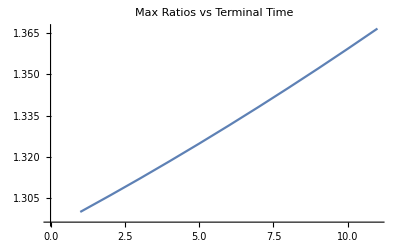

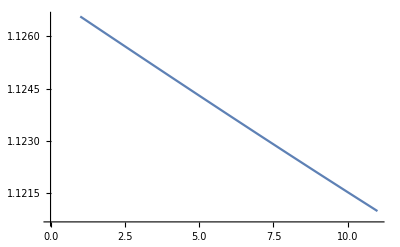

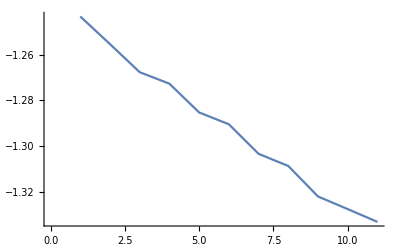

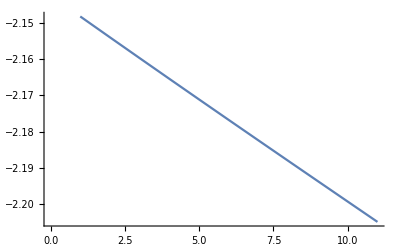

```mathematica
maxrats = computedmmratios[[;;, 1, 1]];
minrats = computedmmratios[[;;, 1, 2]];
maxvecs = computedmmratios[[;;, 2, 1]];
minvecs = computedmmratios[[;;, 2, 2]];
vectoangle[k_] := ArcTan[k[[1]],k[[2]]];

maxangles = Map[vectoangle, maxvecs];
minangles = Map[vectoangle, minvecs];

ListLinePlot[maxrats, PlotLabel -> "Max Ratios vs Terminal Time"   ]
ListLinePlot[minrats, PlotLabel-> "Min Ratios vs Terminal Time"]
ListLinePlot[maxangles, PlotLabel -> "Max Angles vs Terminal Time" ]
maxangles // ListLinePlot
minangles // ListLinePlot
```

```mathematica
energyseteigenvalues[quad_] :=  Eigenvalues[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}]

energysetaxes[quad_] :=
Eigenvectors[{Join[Join[IdentityMatrix[2], {{0,0,0,0},{0,0,0,0}}, 2], {{0,0,0, 0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}], quad[[7;; 12, 7 ;; 12]]}]

vecs = energysetaxes[energyform[1600, n]];
vals = energyseteigenvalues[energyform[1600, n]];




ax1 = vecs[[1]][[1;;2]] * ((comparableenergy / vals[[1]]) // Sqrt)
ax2 = vecs[[2]][[1;;2]] * ((comparableenergy / vals[[2]]) // Sqrt)

Graphics[Ellipsoid[ax1,ax2]]

(** vectoangle[k_] := ArcTan[k[[1]],k[[2]]];
Show[{Graphics[Point[bounds]], Graphics[Circle[{0, 0}, {100, 1000}]], Graphics[Line[5000 AnglePath[{stats[[1]] // vectoangle}]]], Graphics[Line[5000AnglePath[{stats[[2]] // vectoangle}]]]}] **)
```

{1.23468×10^-6,-8.47301×10^-7}

{-1.44888×10^-6,-2.1113×10^-6}

-Graphics-